# Zadanie 1

-3/(√((-1+x)^2+y^2))-1/(√((1+x)^2+y^2))

1

3

1

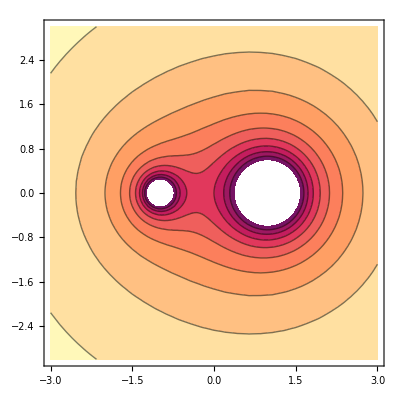

```mathematica
fi[x_,y_ ]=-M1/(√((x+a)^2+y^2))-M2/(√((x-a)^2+y^2))
M1= 1
M2 = 3
a = 1
w1 = ContourPlot[fi[x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
p= {x,0}/.NSolve[D[fi[x,y],x]==0 && D[fi[x,y],y]==0,{x,y},Reals]
```

{{-0.267949,0},{-0.267949,0},{-0.267949,0},{-0.267949,0}}

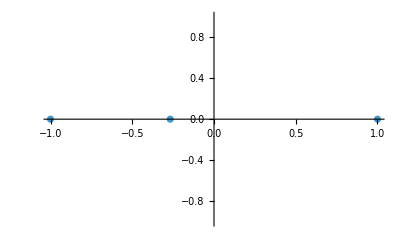

```mathematica
l = ListPlot[{{-a,0},{a,0},p[[1]]}]
```

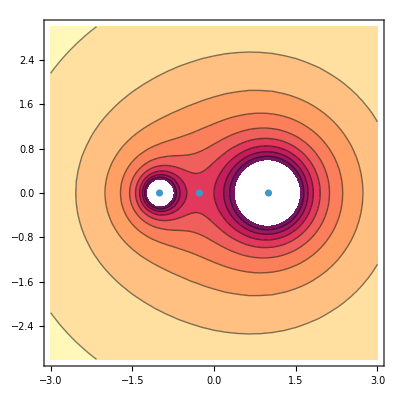

```mathematica
Show[w1,l]
```

# Zadanie 2

```mathematica
x[t_]=(a+b t)Cos[t]
y[t_]= (a+b t) Sin[t]
a=1
b=0.5
tmax=15
```

(1+b t) Cos[t]

(1+b t) Sin[t]

1

0.5

15

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,tmax},PlotRange->{-10,10},Epilog->{Arrow[{x[1.2],y[1.2]},{Vx[1.2],Vy[1.2]}]}]
```

-Graphics-

```mathematica
V1=D[x[t],t]
V2=D[y[t],t]
```

0.5 Cos[t]-(1+0.5 t) Sin[t]

(1+0.5 t) Cos[t]+0.5 Sin[t]

```mathematica
Vx[t_]=V1
Vy[t_]=V2
```

Set::write: Tag Plus in (0.5 Cos[t]-(1+0.5 t) Sin[t])[t_] is Protected.

0.5 Cos[t]-(1+0.5 t) Sin[t]

Set::write: Tag Plus in ((1+0.5 t) Cos[t]+0.5 Sin[t])[t_] is Protected.

(1+0.5 t) Cos[t]+0.5 Sin[t]